```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
Coords = Import["CrossHoleSymData/Coordinates.JSON", "RawJSON"];
Elements = Import["CrossHoleSymData/elements.txt","Table","FieldSeparators"->","];
Elements = Drop[Elements, None, {1}];
UndeformedCoords = Table[{},{i,1,Length[Keys[Coords]]}];
DeformedCoords = Table[{},{i,1,Length[Keys[Coords]]}];
For[i=1, i<=Length[Keys[Coords]], i++,
UndeformedCoords[[i]] = Coords[ToString[i]]["undeformed"];
DeformedCoords[[i]] = Coords[ToString[i]]["deformed"];
];
Nodes = UndeformedCoords;
```

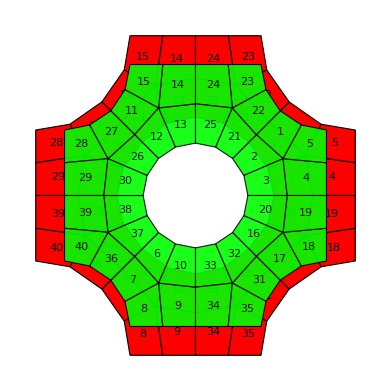

```mathematica
(*Izris deformacij*)
 ELplot= Table[{
	Graphics[{Opacity[0.9],
Green,EdgeForm[Black],Polygon[UndeformedCoords[[Elements[[i]]]]],Black,Text[ToString[i],Mean[UndeformedCoords[[Elements[[i]]]]]]
}]},
	{i,1,Length[Elements]}];

ELplot2= Table[{
	Graphics[{
Red,EdgeForm[Black],Polygon[DeformedCoords[[Elements[[i]]]]],Black,Text[ToString[i],Mean[DeformedCoords[[Elements[[i]]]]]]
}]},
	{i,1,Length[Elements]}];

Show[ ELplot2,ELplot]
```

```mathematica
(*Sile in pomiki*)
```

```mathematica
Force1 = Import["CrossHoleSymData/RF1.txt", "Table", HeaderLines -> 4][[1;;-5,2]];
Force2 = Import["CrossHoleSymData/RF2.txt", "Table", HeaderLines -> 4][[1;;-5,2]];
U1 = Import["CrossHoleSymData/U1.txt", "Table", HeaderLines -> 4][[1;;-5, 2]];
U2 = Import["CrossHoleSymData/U2.txt", "Table", HeaderLines -> 4][[1;;-5, 2]];
ALLWK = Import["CrossHoleSymData/ALLWK.txt", "Table", HeaderLines -> 3][[1;;-5, 2]];
NumericnaIntegracija[force_, U_ ] := Module[{δW = 0* force},
ls = Length[U];
(*Print[δW];*)
For[i = 1, i < ls, i++,
		δW[[i+ 1]] = δW[[i]] + (force[[i+1]]  + force[[i]])/2 * (U[[i+1]] - U[[i]]);
	];
Return[δW];
];
```

```mathematica
δW1 = 2 * NumericnaIntegracija[Force1, U1];(*2 -> saj je sila v obe smeri*)
δW2 = 2 * NumericnaIntegracija[Force2, U2];
δWsk = δW1 + δW2;
```

```mathematica
P1  =ListLinePlot[δW1, AxesOrigin->{1,0}, PlotLegends->{"δW1"}, PlotStyle->{Green}];
P2  =ListLinePlot[δW2, AxesOrigin->{1,0}, PlotLegends->{"δW2 "}, PlotStyle->{Blue,Dashed}];
Pawk = ListLinePlot[ALLWK, AxesOrigin->{1,0}, PlotLegends->{"δALLWK "}, PlotStyle->{Blue,Dashed}];
Psk  =ListLinePlot[δWsk, AxesOrigin->{1,0}, PlotLegends->{"δWsk - skupno delo"}, PlotStyle->Red];
```

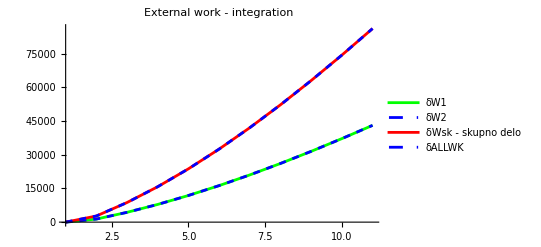

```mathematica
Show[P1, P2, Psk,Pawk, PlotRange -> All, PlotLabel -> "External work - integration"]
```

```mathematica
(*Notranje delo -> δv*)

F = Import["CrossHoleSymData/Grad_PHANTOM.JSON", "RawJSON"];
Frames = Length[Keys[F]] -1;
nelements = Length[Keys[F["1"]]];
ngp = Length[Keys[F["1"][["1"]]]];
S = Import["CrossHoleSymData/Stress.JSON", "RawJSON"];

determinants = Table[{},{i,1,nelements}];
d = 0.8; (*mat. thick*)

{Keys[F], Keys[S]} // MatrixForm
```

({0,1,2,3,4,5,6,7,8,9,10,11}
{0,1,2,3,4,5,6,7,8,9,10})

```mathematica
δWint = {};
δWintL = {};
For[frame = 0, frame <= Frames-1, frame++,
Print["Frame: ", frame];
δWinte = 0;
δWinteL = 0;
For[element=1, element <= nelements, element++,
	(*Determinanta elementa*)
	det = {};
	Subscript[𝒯, 1] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {-1,-1};
	Subscript[𝒯, 2] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {1,-1};
	Subscript[𝒯, 3] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {1,1};
	Subscript[𝒯, 4] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {-1,1};
	Subscript[ψ, i_][𝒳_, 𝒴_] := 1/4(1 + Subscript[𝒯, i][[1]] * 𝒳) *(1 + Subscript[𝒯, i][[2]]  * 𝒴);
	x = Nodes[[Elements[[element]]]][[;;,1]];
	y = Nodes[[Elements[[element]]]][[;;,2]];
	
	X[𝒳_, 𝒴_]  := Sum[Subscript[ψ, i][𝒳, 𝒴] x[[i]],{i,1,4}];
	Y[𝒳_, 𝒴_]  := Sum[Subscript[ψ, i][𝒳, 𝒴] y[[i]],{i,1,4}];
	J[𝒳_, 𝒴_]  = ({{D[X[𝒳, 𝒴], 𝒳], D[Y[𝒳, 𝒴], 𝒳]}, {D[X[𝒳, 𝒴], 𝒴], D[Y[𝒳, 𝒴], 𝒴]}});
	
	det = Append[det,
	{Det[J[-1/(√3),-1/(√3)]],
	Det[J[1/(√3),-1/(√3)]],
	Det[J[-1/(√3),1/(√3)]],
	Det[J[1/(√3),1/(√3)]]}];
	determinants[[element]] = Sum[det[[1,i]],{i,1,4}]; (*Preverjanje povrsin*)
	(*Print["Element: ", element, " Det: ", determinants[[element]]];*)
	
	δWintgp = 0;
	δWintgpL = 0;
	For[gp=1, gp <= ngp, gp++,
		(*Print["Gauss Int. Point: ", gp];*)
		(*Gradient: *)
		Fgp = F[ToString[frame]][ToString[element]][ToString[gp]][["F"]];
		F11 = Fgp[[1]];
		F12 = Fgp[[2]];
		F21 = Fgp[[3]];
		F22 = Fgp[[4]];
		F33 = Fgp[[5]]/d;
		
		(*Stress*)
		σ = S[[ToString[frame]]][[ToString[element]]][[ToString[gp]]][["S"]];
		(*σ -> S11, S22, S33, S12*)
		σ11 =σ[[1]];
		σ12 =σ[[4]]; (*Drugi stolpec*)
		σ22 =σ[[2]];

		(*1.st Piola Kirchoff Stress*)
		p11 = F33 (F22 σ11 - F12 σ12);
		p12 = - F21 F33 σ11 + F11 F33 σ12;
		p21 = F33 (F22 σ12 - F12 σ22);
		p22 = -F21 F22 σ12 + F11 F33 σ22;

		(*Velocity gradient L or δv*)
		(*δv -> simple*)
		Δt = 1/Frames;
		Fnf = F[ToString[frame+1]][ToString[element]][ToString[gp]][["F"]];(*Fnf -> next frame*)
		Fdot = δvf = 1/Δt(Fnf - Fgp);
		δv11 = δvf[[1]];
		δv12 = δvf[[2]];
		δv21 = δvf[[3]];
		δv22 = δvf[[4]];
		δv33 = δvf[[5]];
		δW = (p11 δv11 + p12 δv12 + p21 δv21 + p22 δv22 ) *det[[1,gp]] * d;
		δWintgp += δW; (*Sum dela vseh gaussovih tock*)

		(*L -> correct way*)
		Fmat = ({{F11, F12, 0}, {F21, F22, 0}, {0, 0, F33}});
		If[frame ==0, Finv =({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}}),Finv = Inverse[Fmat]];
		δvmat = ({{δv11, δv12, 0}, {δv21, δv22, 0}, {0, 0, δv33}});

		L = δvmat.Finv;
		δWL = (p11 L[[1,1]] + p12 L[[1,2]] + p21 L[[2,1]] + p22 L[[2,2]]) *det[[1,gp]] * d;
		δWintgpL += δWL
		(*Potrebno integrirati!!!! *)
		
];(*gauss point*)
δWinte += δWintgp;
δWinteL += δWintgpL;

];(*element*)
δWint = Append[δWint, δWinte];
δWintL = Append[δWintL, δWinteL];
]; (*Frame*)
```

Frame: 0

Frame: 1

Frame: 2

Frame: 3

Frame: 4

Frame: 5

Frame: 6

Frame: 7

Frame: 8

Frame: 9

Frame: 10

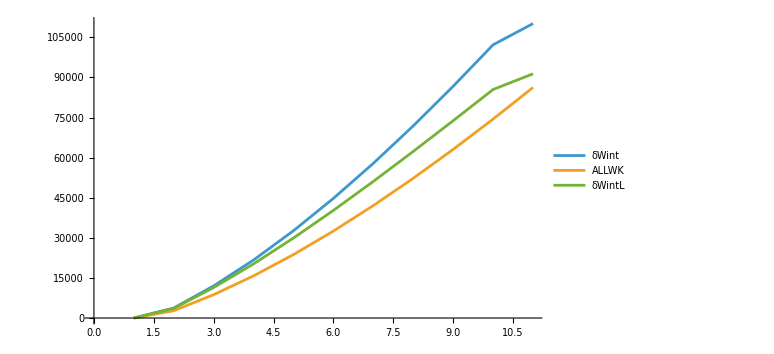

```mathematica
NumericnaIntegracija[X_, Y_ ] := Module[{I = 0* X},
ls = Length[Y];
(*Print[δW];*)
For[i = 1, i < ls, i++,
		I[[i+ 1]] = I[[i]] + (Y[[i+1]]  + Y[[i]])/2 * (X[[i+1]] - X[[i]]);
	];
Return[I];
];

t = Table[i*0.1, {i,0,10}];
δWint = NumericnaIntegracija[t, δWint];
δWintL = NumericnaIntegracija[t, δWintL];
ListLinePlot[{δWint, ALLWK, δWintL},PlotLegends->{"δWint", "ALLWK", "δWintL"}]
```